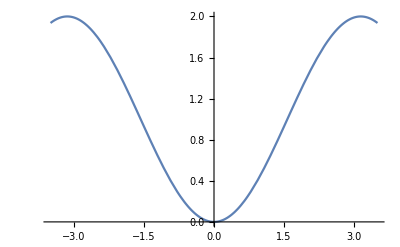

```mathematica
LJ[w_]:=-Cos[w]+1
Plot[LJ[0.1,x],{x,-3.5,3.5}, PlotRange->All]
```

```mathematica
tp2=Flatten@{Subdivide[0,3.14,3],Subdivide[3.15,6.28,3]}
```

{0.,1.04667,2.09333,3.14,3.15,4.19333,5.23667,6.28}

```mathematica
test = -tp2
```

{0.,-1.04667,-2.09333,-3.14,-3.15,-4.19333,-5.23667,-6.28}

```mathematica
period[lo_?NumericQ, hi_?NumericQ]:=period[lo,hi]=(1/Sqrt[2])*NIntegrate[1/(Sqrt[LJ[hi]-LJ[x]]),{x,lo,hi}]
periods = Thread[period[0,tp2]];
energy[lo_?NumericQ, hi_?NumericQ, c_?NumericQ]:=energy[lo,hi,c]=(2*Sqrt[2])*NIntegrate[Sqrt[LJ[hi]-LJ[x]] + 2* c*(-0 - LJ[hi]),{x,lo,hi}]
energies = Thread[energy[test,tp2,periods]];

totenergy = Thread[LJ[test]]


NIntegrate[1/(Sqrt[-LJ[x]+LJ[3]]),{x,0,3}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.13159289650026}. NIntegrate obtained 10.6325-4.11665 ⅈ and 1.16549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.0966}. NIntegrate obtained 3.02921-4.74825 ⅈ and 0.0640888 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.05339}. NIntegrate obtained 2.34348-6.06406 ⅈ and 0.119187 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.,0.49954,1.49908,2.,1.99996,1.49606,0.499412,5.07309×10^-6}

5.71185

```mathematica
LJ[0.1,0.1]
```

0.00499583

```mathematica
periods
```

{0.,1.57088,1.57115,1.57159,1.57221,1.57301,1.57398,1.57514,1.57647,1.57798,1.57968,1.58155,1.58362,1.58586,1.58829,1.59091,1.59372,1.59672,1.59991,1.6033,1.60689,1.61067,1.61466,1.61885,1.62326,1.62787,1.63269,1.63774,1.64301,1.6485,1.65422,1.66017,1.66636,1.67279,1.67948,1.68641,1.6936,1.70106,1.70878,1.71678,1.72506,1.73364,1.74251,1.75168,1.76117,1.77099,1.78113,1.79161,1.80245,1.81365,1.82522,1.83717,1.84953,1.8623,1.87549,1.88913,1.90322,1.91779,1.93285,1.94843,1.96454,1.98121,1.99846,2.01631,2.0348,2.05395,2.0738,2.09438,2.11573,2.13788,2.16088,2.18478,2.20963,2.23549,2.26241,2.29047,2.31973,2.3503,2.38224,2.41567,2.4507,2.48746,2.52609,2.56675,2.60964,2.65496,2.70296,2.75394,2.80822,2.8662,2.92837,2.9953,3.06769,3.14643,3.23263,3.32774,3.43366,3.553,3.68947,3.84854,4.03888}

```mathematica
totenergy
```

{0,1-Cos[3/100],1-Cos[3/50],1-Cos[9/100],1-Cos[3/25],1-Cos[3/20],1-Cos[9/50],1-Cos[21/100],1-Cos[6/25],1-Cos[27/100],1-Cos[3/10],1-Cos[33/100],1-Cos[9/25],1-Cos[39/100],1-Cos[21/50],1-Cos[9/20],1-Cos[12/25],1-Cos[51/100],1-Cos[27/50],1-Cos[57/100],1-Cos[3/5],1-Cos[63/100],1-Cos[33/50],1-Cos[69/100],1-Cos[18/25],1-Cos[3/4],1-Cos[39/50],1-Cos[81/100],1-Cos[21/25],1-Cos[87/100],1-Cos[9/10],1-Cos[93/100],1-Cos[24/25],1-Cos[99/100],1-Cos[51/50],1-Cos[21/20],1-Cos[27/25],1-Cos[111/100],1-Cos[57/50],1-Cos[117/100],1-Cos[6/5],1-Cos[123/100],1-Cos[63/50],1-Cos[129/100],1-Cos[33/25],1-Cos[27/20],1-Cos[69/50],1-Cos[141/100],1-Cos[36/25],1-Cos[147/100],1-Cos[3/2],1-Cos[153/100],1-Cos[39/25],1-Cos[159/100],1-Cos[81/50],1-Cos[33/20],1-Cos[42/25],1-Cos[171/100],1-Cos[87/50],1-Cos[177/100],1-Cos[9/5],1-Cos[183/100],1-Cos[93/50],1-Cos[189/100],1-Cos[48/25],1-Cos[39/20],1-Cos[99/50],1-Cos[201/100],1-Cos[51/25],1-Cos[207/100],1-Cos[21/10],1-Cos[213/100],1-Cos[54/25],1-Cos[219/100],1-Cos[111/50],1-Cos[9/4],1-Cos[57/25],1-Cos[231/100],1-Cos[117/50],1-Cos[237/100],1-Cos[12/5],1-Cos[243/100],1-Cos[123/50],1-Cos[249/100],1-Cos[63/25],1-Cos[51/20],1-Cos[129/50],1-Cos[261/100],1-Cos[66/25],1-Cos[267/100],1-Cos[27/10],1-Cos[273/100],1-Cos[69/25],1-Cos[279/100],1-Cos[141/50],1-Cos[57/20],1-Cos[72/25],1-Cos[291/100],1-Cos[147/50],1-Cos[297/100],1-Cos[3]}

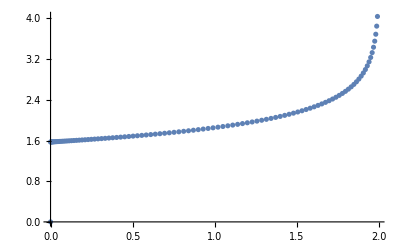

```mathematica
data=Transpose@{totenergy, periods};
ListPlot[data,DataRange->{1,20}]
```

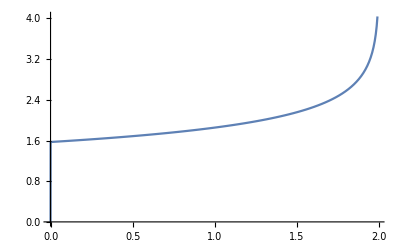

```mathematica
ListLinePlot[data, DataRange->{1,20}]
```

```mathematica
data
```

{{0.,0.},{1.57088,0.00129369},{1.57115,0.00469422},{1.57159,0.00947977},{1.57221,0.0149275},{1.57301,0.0203138},{1.57398,0.0249145},{1.57514,0.0280052},{1.57647,0.0288616},{1.57798,0.0267596},{1.57968,0.0209755},{1.58155,0.0107867},{1.58362,-0.00452873},{1.58586,-0.0256911+4.25077×10^-27 ⅈ},{1.58829,-0.0534195},{1.59091,-0.0884311+4.7845×10^-27 ⅈ},{1.59372,-0.131441},{1.59672,-0.183163+5.13068×10^-27 ⅈ},{1.59991,-0.244307+1.11903×10^-26 ⅈ},{1.6033,-0.315581},{1.60689,-0.397691},{1.61067,-0.491339+4.88761×10^-27 ⅈ},{1.61466,-0.597225+1.39638×10^-26 ⅈ},{1.61885,-0.716045},{1.62326,-0.848492},{1.62787,-0.995255},{1.63269,-1.15702+1.63522×10^-26 ⅈ},{1.63774,-1.33447+2.44002×10^-26 ⅈ},{1.64301,-1.52828},{1.6485,-1.73913},{1.65422,-1.96768+1.81604×10^-26 ⅈ},{1.66017,-2.21462+2.82088×10^-26 ⅈ},{1.66636,-2.48059},{1.67279,-2.76626},{1.67948,-3.07229+1.91725×10^-26 ⅈ},{1.68641,-3.39932+3.15759×10^-26 ⅈ},{1.6936,-3.74802+4.14543×10^-26 ⅈ},{1.70106,-4.11902+5.03638×10^-26 ⅈ},{1.70878,-4.51297},{1.71678,-4.93052},{1.72506,-5.3723},{1.73364,-5.83895},{1.74251,-6.33111+1.7574×10^-26 ⅈ},{1.75168,-6.84941+3.64789×10^-26 ⅈ},{1.76117,-7.3945+4.9645×10^-26 ⅈ},{1.77099,-7.96701+6.0936×10^-26 ⅈ},{1.78113,-8.56757},{1.79161,-9.19684},{1.80245,-9.85545},{1.81365,-10.5441},{1.82522,-11.2633},{1.83717,-12.0139+3.81406×10^-26 ⅈ},{1.84953,-12.7964+5.515×10^-26 ⅈ},{1.8623,-13.6117+6.88942×10^-26 ⅈ},{1.87549,-14.4602+8.10438×10^-26 ⅈ},{1.88913,-15.3429},{1.90322,-16.2603},{1.91779,-17.2133},{1.93285,-18.2026},{1.94843,-19.2289+3.55545×10^-26 ⅈ},{1.96454,-20.2932+5.72723×10^-26 ⅈ},{1.98121,-21.3962+7.34693×10^-26 ⅈ},{1.99846,-22.539+8.72438×10^-26 ⅈ},{2.01631,-23.7223},{2.0348,-24.9472},{2.05395,-26.2147},{2.0738,-27.5259},{2.09438,-28.8821},{2.11573,-30.2844+5.54806×10^-26 ⅈ},{2.13788,-31.7342},{2.16088,-33.233+8.90929×10^-26 ⅈ},{2.18478,-34.7823},{2.20963,-36.3838+1.13839×10^-25 ⅈ},{2.23549,-38.0395},{2.26241,-39.7513+1.34336×10^-25 ⅈ},{2.29047,-41.5214},{2.31973,-43.3525},{2.3503,-45.2471+7.01212×10^-26 ⅈ},{2.38224,-47.2084},{2.41567,-49.2397+9.90056×10^-26 ⅈ},{2.4507,-51.345},{2.48746,-53.5284+1.2039×10^-25 ⅈ},{2.52609,-55.7951},{2.56675,-58.1504+1.37313×10^-25 ⅈ},{2.60964,-60.6009+3.88741×10^-26 ⅈ},{2.65496,-63.154},{2.70296,-65.8182+7.68134×10^-26 ⅈ},{2.75394,-68.6037},{2.80822,-71.5223+9.89271×10^-26 ⅈ},{2.8662,-74.5882},{2.92837,-77.8182},{2.9953,-81.2331},{3.06769,-84.8582},{3.14643,-88.7252},{3.23263,-92.8744},{3.32774,-97.3578},{3.43366,-102.245},{3.553,-107.63},{3.68947,-113.647},{3.84854,-120.496},{4.03888,-128.489}}